# Numerical methods for ⅈ u_t+1/2 u_xx+|u|^2 u=0 on a<x<b with periodic BC.

## Method of Lines

We need to define the points at which we are going to approximate solutions.   We need to approximate the pieces in the PDE we want to solve using these values.  Approximating derivatives from sampled values!

```mathematica
Clear[D2s,D1c,D1f,D1b,D2w,D2v,Δx,h,n]
D2s[Δx_,n_]:=Δx^-2*SparseArray[{
Band[{1,1}]->-2.0,
Band[{1,2}]->1.0,
Band[{2,1}]->1.0,
{1,n}->1.0,{n,1}->1.0},{n,n}];
D1c[Δx_,n_]:=(2 Δx)^-1 SparseArray[{
Band[{2,1}]->-1.0,
Band[{1,2}]->1.0,
{1,n}->-1.0,{n,1}->1.0},{n,n}];
D1f[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->1.0,
Band[{2,1}]->-1.0,
{1,n}->-1.0},{n,n}];
D1b[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->-1.0,
Band[{1,2}]->1.0,
{n,1}->1.0},{n,n}];
D2w[Δx_,n_]:=(12 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,
Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,
Band[{3,1}]->-1.0,
Band[{1,n}]->16.0,
Band[{n,1}]->16.0,
Band[{1,n-1}]->-1.0,
Band[{n-1,1}]->-1.0
},{n,n}];
D2v[Δx_,n_]:=(180 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-490.0,
Band[{1,2}]->270.0,
Band[{2,1}]->270.0,
Band[{1,3}]->-27.0,
Band[{3,1}]->-27.0,
Band[{1,4}]->2.0,
Band[{4,1}]->2.0,
Band[{1,n}]->270.0,
Band[{n,1}]->270.0,
Band[{1,n-1}]->-27.0,
Band[{n-1,1}]->-27.0,
Band[{1,n-2}]->2.0,
Band[{n-2,1}]->2.0
},{n,n}];
n=10;
TabView[{
"D2s"->MatrixForm[D2s[h,n]],
"D1c"->MatrixForm[D1c[h,n]],
"D1f"->MatrixForm[D1f[h,n]],
"D1b"->MatrixForm[D1b[h,n]],
"D2w"->MatrixForm[D2w[h,n]],
"D2v"->MatrixForm[D2v[h,n]]
}]
```

123456

```mathematica
L=12;
{a,b}={-L,L};
n=2*512;
Δx=2.0 L/n;
x[j_]:= a+ Δx j
f[x_]:=2+1.2 Sin[3 π x/L]-0.4 Cos[2 π x/L]+3.2Sin[5 π x/L]
fVec=Table[f[x[j]],{j,1,n}];
D1fVec=Table[f'[x[j]],{j,1,n}];
D2fVec=Table[f''[x[j]],{j,1,n}];
TabView[{
"f"->Show[Plot[f[x],{x,a,b},PlotStyle->Red],
ListPlot[fVec,DataRange->{a+Δx,b}]],
"f'"->Show[Plot[f'[x],{x,a,b},PlotStyle->Red],
ListPlot[D1c[Δx,n].fVec,DataRange->{a+Δx,b}]],
"f''"->Show[Plot[f''[x],{x,a,b},PlotStyle->Red],
ListPlot[D2s[Δx,n].fVec,DataRange->{a+Δx,b}]],
"|f'-D_(1?).f|" -> ListLogPlot[ 
Abs[{D1fVec-D1c[Δx,n].fVec,D1fVec-D1b[Δx,n].fVec,D1fVec-D1f[Δx,n].fVec}],
DataRange->{-L,L},PlotLegends->{"c","b","f","orig"},GridLines->Automatic,
PlotRange->All],
"|f''-D_(2?).f|" -> ListLogPlot[ 
Abs[{D2fVec-D2s[Δx,n].fVec,D2fVec-D2w[Δx,n].fVec,D2fVec-D2v[Δx,n].fVec}],
DataRange->{-L,L},PlotRange->All,PlotLegends->{"s","w","v"},GridLines->Automatic]
}]
```

12345

We need to understand (in as many ways as possible) the effects of our different approximate differentiation matrices.

Here is what a MOL formulation looks like for the heat equation
	u_t=u_xx with u(x,0)=f(x)
on the interval {a,b} with periodic boundary conditions.  Approximate the solution at the spatial points
	x_j=a+j Δx
with Δx=(b-a)/n  and assemble the approximations
	u_j(t)≈u(a+j Δx,t)
into  the vector u(t)=(u_1(t),…,u_n(t)) the approximate the second derivative operator with your choice of the second derivative matrices. You get 
	u'=D_2.u  and u(0)=(f(x_1),f(x_2),…,f(x_n))

```mathematica
L=12;{a,b}={-L,L};
n=2*128;
Δx=2.0 L/n;
x[j_]:= a+ Δx j
f[x_]:=2+1.2 Sin[3 π x/L]-0.4 Cos[2 π x/L]+3.2Sin[5 π x/L]
u0=Table[ f[x[j]],{j,1,n}];
D2=D2v[Δx,n];
TMax=3;
uSol=NDSolveValue[{u'[t]==D2.u[t],u[0]==u0},u,{t, 0, TMax}]
TSteps=50;
Data=Table[uSol[t],{t,0, TMax, TMax/TSteps}];
ListPlot3D[Data,PlotRange->All];
```

InterpolatingFunction[{{0., 3.}}, <>]

```mathematica
TSteps=100;
Data=Table[uSol[t],{t,0, TMax, TMax/TSteps}];
Dimensions[Data];
TabView[{
"3d"->ListPlot3D[Data,PlotRange->All,
AxesLabel->{"x","t","u"},DataRange->{{-L,L},{0,TMax}}],
"Contours"->ListContourPlot[Data,PlotRange->All,
FrameLabel->{"x","t"},DataRange->{{-L,L},{0,TMax}},
PlotLegends->Automatic]
}]
```

12

## Spectral Methods: Discussion

We need to understand and check the Fourier solvers for linear PDEs.  The first thing we need to understand is the order that our FFT puts the pieces in.   We decided we are doing a periodic problem on the interval -L<x<L.  We are going to assume our data is of length n with x_1=-L+Δx, x_2=-L+2 Δx, and x_n=-L+n Δx=L

```mathematica
FourierShift[data_?ArrayQ]:=FourierShift[data,All]
FourierShift[data_?ArrayQ,dim_]:=Block[
  {n=ConstantArray[0,ArrayDepth@data]},
  n[[dim]]=Check[
      Ceiling[Dimensions[data]/2][[dim]],
      Return[data,Block]
  ];
  RotateLeft[data,n]
]
```

```mathematica
TabView[{
"Sin"->Plot[ {Sin[ π x/L],Sin[2 π x/L],Sin[3 π x/L],Sin[4 π x/L]},{x,-L,L},
PlotLegends->{1,2,3,4}],
"Cos"->Plot[ {Cos[ π x/L],Cos[2 π x/L],Cos[3 π x/L],Cos[4 π x/L]},{x,-L,L},
PlotLegends->{1,2,3,4}],
"Sin+Cos"->Plot[ {√(2^2+1^2),2 Sin[π x/L]+Cos[ π x/L],
Cos[2 π x/L]+2 Sin[2 π x/L],Cos[3 π x/L],Cos[4 π x/L]},{x,-L,L},
PlotLegends->{1,2,3,4}]
}]
```

123

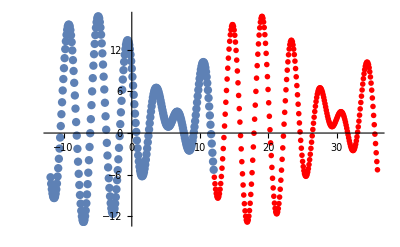

```mathematica
L=12;
m=128;n=2*m;
Δx=2.0L/n;
f[x_]:=2+ 7.3 Cos[5π x/L]-7.7 Sin[6π x/L]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
Show[
ListPlot[fVec,
PlotStyle->PointSize[0.015],
DataRange->{-L+Δx,L}],
ListPlot[fVec,PlotStyle->Directive[PointSize[0.01],Red],
DataRange->{L+Δx,3L}],
PlotRange->All
]
```

```mathematica
fHat=Fourier[fVec];
NewfHat=FourierShift[fHat];
TabView[{
"orig"->ListPlot[{Re[fHat],Im[fHat],Abs[fHat]},
PlotLegends->{"re","im","abs"},PlotRange->All,
DataRange->{1,2m},GridLines->Automatic,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]}],
"orig-zoom"->ListPlot[{Re[fHat],Im[fHat],Abs[fHat]},
PlotLegends->{"re","im","abs"},PlotRange->{{1,11},All},
DataRange->{1,2m},GridLines->Automatic,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]}],
"new"->ListPlot[{Re[NewfHat],Im[NewfHat],Abs[NewfHat]},
PlotLegends->{"re","im"},PlotRange->All,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]},
DataRange->{-m-1,m},GridLines->Automatic],
"new-Zoom"->ListPlot[{Re[NewfHat],Im[NewfHat],Abs[NewfHat]},
PlotLegends->{"re","im"},PlotRange->{{-10,10},All},PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]},
DataRange->{-m-1,m},GridLines->Automatic]
}]
```

1234

### DFT and FFT

The FFT is simply a family of efficient recursive implementation of the DFT
	X_k=∑_(j=0)^(n-1) x_j ⅇ^(-ⅈ 2π k/n j)
it splits the n-vector x_(0:n-1) into a sum of wiggles
	x_j=1/n∑_(k=0)^(n-1) X_j ⅇ^(ⅈ 2π j/n k).
It is possible (and common) to put the scaling 1/n in different places!  Since most linear algebra starts at counting at 1.  The same transform recipe can look like
	   X_k=∑_(j=1)^n x_j ⅇ^(-ⅈ 2π (k-1)/n(j-1)).
All this does is make counting the wiggles harder. 
1) In the FFT the DC component turns up in the first entry of the vector.  This first entry should really be labelled with a zero for zero wiggles.
2) All the wiggle counts are off by one as a result.
3) Aliasing means that the highest wiggle counts can be appropriately interpreted as negative wiggle counts since.
	ⅇ^(-ⅈ 2π(k/n j))=ⅇ^(-ⅈ 2π(k/n j)).ⅇ^(2π ⅈ)=ⅇ^(-ⅈ 2π(k/n j-1))=ⅇ^(-ⅈ 2π(k/n j-1))
4) The FFT of a signal with lots of low wiggle counts has symmetry (odd and even) about the mid points.
5) The real and imaginary parts of the FFT encode the phase shift of a wave. 
Lots of engineering fields like the symmetric or almost symmetric version.

```mathematica
L=12;
m=128;n=2*m;
Δx=2.0L/n;
f[x_]:=2+ 7.3 Cos[6π x/L]-7.7 Sin[6π x/L]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
FData=Fourier[fVec];
TabView[{
"All"->ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->All],
"Low"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{1,10},All},
PlotStyle->PointSize[0.02]],
"High"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{n-10,n},All},
PlotStyle->PointSize[0.02]]
}]
```

123

## Phase Shifts and Spectral Methods

We want to be able to understand what differentiating with respect to x looks like in transform land.  We are going to use the definition pair counting from j=1 and k=1 with the scaling on the inverse transform
	U_k=∑_(j=1)^n u_j ⅇ^(-ⅈ 2π ((k-1)(j-1))/n)
and
	u_j=1/n∑_(k=1)^n U_k ⅇ^(ⅈ 2π ((k-1)(j-1))/n)
There are a couple of way to see what this looks like.  I am going to try to keep it simple.

Since the derivative is 
	 u'(x)=lim_(h->0) (u(x+h)-u(x))/h
we can work out what happens when we sample and take the FFT by shift then subtracting and scaling.  This is all easier (and more natural) in the complex exponential version. To shift the sines and cosines over by a shift h we do 
	cos(𝕜 x)+ⅈ sin( 𝕜 x)=ⅇ^(ⅈ 𝕜 x)→ⅇ^(ⅈ 𝕜 (x+h))=ⅇ^(ⅈ 𝕜)e^(ⅈ 𝕜 h)
Using the version starting with the index 1 we have
	u(x_(j+h))=1/n∑_(k=1)^n U_k ⅇ^(ⅈ 2π ((k-1)h)/n)ⅇ^(ⅈ 2π ((k-1)(j-1))/n)
where we have used to short hand j+h subscript to indicate moving the sample points to 
	x_(j+h)=a+(j+h)Δx
This is easy enough to implement and check

3/16

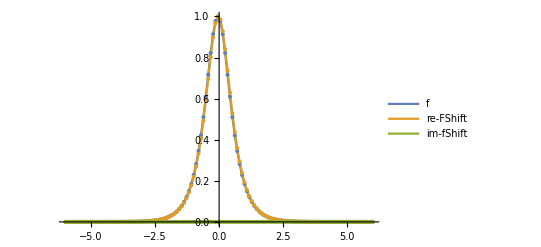

```mathematica
n=128;
baseshift=Table[ⅇ^(2.0π ⅈ (k-1)/n),{k,1,n}];
L=6;
Δx=2L/n;
x[j_]:=-L+j Δx
f[x_]:= Sech[2.3 x]
fVec=Table[f[x[j]],{j,1,n}];
FData=Fourier[fVec];
h=2 Δx
ShiftedFData=baseshift^h*FData;
ShiftedfVec=InverseFourier[ShiftedFData];
ListPlot[{fVec, Re[ShiftedfVec],Im[ShiftedfVec]},PlotRange->All,Joined->True,Mesh->All,DataRange->{-L,L},
PlotLegends->{"f","re-FShift","im-fShift"}]
```

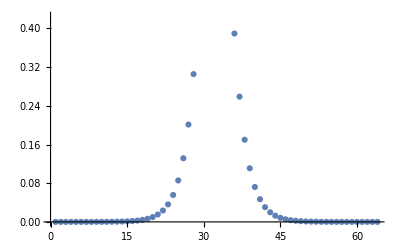

12345

```mathematica
fShiftVec=Table[f[x[j]+h],{j,1,n}] ;
FShiftData=Fourier[fShiftVec];
TabView[{
"Data"->ListPlot[ {Re[fVec],Re[fShiftVec]},
PlotRange->All,PlotLegends->{"f","f(x+h)"}],
"FData"->ListPlot[ {Re[FData],Im[FData],Re[FShiftData],Im[FShiftData]},
PlotRange->All,PlotLegends->{"re(F)","im(F)", "re(Fs)","im(Fs)"}],
"FData-Low"->ListPlot[ {Re[FData],Im[FData],Re[FShiftData],Im[FShiftData]},
PlotLegends->{"re(F)","im(F)", "re(Fs)","im(Fs)"},
PlotRange->{{1,20},All},PlotStyle->PointSize[0.01]],
"FData Ratio"->ListPlot[ {Abs[FData/FShiftData],Arg[FData/FShiftData]},
PlotLegends->{"Abs(F/Fs)","Arg(F/Fs)"},
PlotRange->All,PlotStyle->PointSize[0.01]],
"Abs[FData]"->ListLogPlot[ Abs[FData],
PlotLegends->{"AbsF"},
PlotRange->All,PlotStyle->PointSize[0.01]]
},4]
```

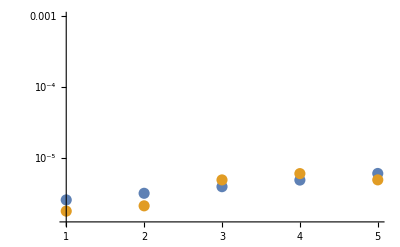

```mathematica
ListPlot[{fVec, InverseFourier[Chop[FData,10^-5]]},PlotRange->All];
ListLogPlot[{fVec, InverseFourier[Chop[FData,10^-5]]},PlotRange->{{1,5},{0,0.001}},
PlotStyle->PointSize[0.02]]
```

## Break

```mathematica
FData=Fourier[fVec];
ShiftedFData=phase*FData;
Map[Dimensions,{FData,phase,ShiftedFData}]
ShiftedFVec=InverseFourier[ShiftedFData];
ShiftedFVec⟦60⟧
ListPlot[Chop[ShiftedFVec]]
```

6

{{128},{128},{128}}

0.705762-5.10478×10^-10 ⅈ

-Graphics-

```mathematica
ListPlot[{fVec, Chop[ShiftedFVec]},PlotRange->All]
```

```mathematica
ChopShiftedFVec
```

{2.44852×10^-6+5.10478×10^-10 ⅈ,3.06998×10^-6-5.10478×10^-10 ⅈ,3.78906×10^-6+5.10478×10^-10 ⅈ,4.71489×10^-6-5.10478×10^-10 ⅈ,5.83858×10^-6+5.10478×10^-10 ⅈ,7.25243×10^-6-5.10478×10^-10 ⅈ,8.99016×10^-6+5.10478×10^-10 ⅈ,0.00001116-5.10478×10^-10 ⅈ,0.0000138398+5.10478×10^-10 ⅈ,0.0000171752-5.10478×10^-10 ⅈ,0.0000213037+5.10478×10^-10 ⅈ,0.0000264343-5.10478×10^-10 ⅈ,0.0000327916+5.10478×10^-10 ⅈ,0.0000406859-5.10478×10^-10 ⅈ,0.0000504732+5.10478×10^-10 ⅈ,0.0000626219-5.10478×10^-10 ⅈ,0.0000776883+5.10478×10^-10 ⅈ,0.0000963856-5.10478×10^-10 ⅈ,0.000119577+5.10478×10^-10 ⅈ,0.000148354-5.10478×10^-10 ⅈ,0.000184051+5.10478×10^-10 ⅈ,0.000228343-5.10478×10^-10 ⅈ,0.000283289+5.10478×10^-10 ⅈ,0.000351461-5.10478×10^-10 ⅈ,0.000436033+5.10478×10^-10 ⅈ,0.000540961-5.10478×10^-10 ⅈ,0.000671134+5.10478×10^-10 ⅈ,0.000832635-5.10478×10^-10 ⅈ,0.001033+5.10478×10^-10 ⅈ,0.00128158-5.10478×10^-10 ⅈ,0.00158997+5.10478×10^-10 ⅈ,0.00197257-5.10478×10^-10 ⅈ,0.00244725+5.10478×10^-10 ⅈ,0.00303614-5.10478×10^-10 ⅈ,0.00376675+5.10478×10^-10 ⅈ,0.00467316-5.10478×10^-10 ⅈ,0.00579767+5.10478×10^-10 ⅈ,0.00719278-5.10478×10^-10 ⅈ,0.00892356+5.10478×10^-10 ⅈ,0.0110708-5.10478×10^-10 ⅈ,0.0137346+5.10478×10^-10 ⅈ,0.0170392-5.10478×10^-10 ⅈ,0.0211387+5.10478×10^-10 ⅈ,0.0262238-5.10478×10^-10 ⅈ,0.0325312+5.10478×10^-10 ⅈ,0.0403537-5.10478×10^-10 ⅈ,0.0500533+5.10478×10^-10 ⅈ,0.062077-5.10478×10^-10 ⅈ,0.076975+5.10478×10^-10 ⅈ,0.0954217-5.10478×10^-10 ⅈ,0.118238+5.10478×10^-10 ⅈ,0.146414-5.10478×10^-10 ⅈ,0.18112+5.10478×10^-10 ⅈ,0.223707-5.10478×10^-10 ⅈ,0.275656+5.10478×10^-10 ⅈ,0.338454-5.10478×10^-10 ⅈ,0.413322+5.10478×10^-10 ⅈ,0.500713-5.10478×10^-10 ⅈ,0.599484+5.10478×10^-10 ⅈ,0.705762-5.10478×10^-10 ⅈ,0.811789+5.10478×10^-10 ⅈ,0.905565-5.10478×10^-10 ⅈ,0.972516+5.10478×10^-10 ⅈ,0.999768-5.10478×10^-10 ⅈ,0.981461+5.10478×10^-10 ⅈ,0.921572-5.10478×10^-10 ⅈ,0.831973+5.10478×10^-10 ⅈ,0.727314-5.10478×10^-10 ⅈ,0.620325+5.10478×10^-10 ⅈ,0.519633-5.10478×10^-10 ⅈ,0.429806+5.10478×10^-10 ⅈ,0.352432-5.10478×10^-10 ⅈ,0.287302+5.10478×10^-10 ⅈ,0.233299-5.10478×10^-10 ⅈ,0.188961+5.10478×10^-10 ⅈ,0.152792-5.10478×10^-10 ⅈ,0.12341+5.10478×10^-10 ⅈ,0.0996063-5.10478×10^-10 ⅈ,0.0803564+5.10478×10^-10 ⅈ,0.064807-5.10478×10^-10 ⅈ,0.0522561+5.10478×10^-10 ⅈ,0.0421305-5.10478×10^-10 ⅈ,0.033964+5.10478×10^-10 ⅈ,0.027379-5.10478×10^-10 ⅈ,0.02207+5.10478×10^-10 ⅈ,0.01779-5.10478×10^-10 ⅈ,0.0143398+5.10478×10^-10 ⅈ,0.0115586-5.10478×10^-10 ⅈ,0.00931679+5.10478×10^-10 ⅈ,0.00750974-5.10478×10^-10 ⅈ,0.00605316+5.10478×10^-10 ⅈ,0.00487909-5.10478×10^-10 ⅈ,0.00393274+5.10478×10^-10 ⅈ,0.00316994-5.10478×10^-10 ⅈ,0.00255509+5.10478×10^-10 ⅈ,0.0020595-5.10478×10^-10 ⅈ,0.00166004+5.10478×10^-10 ⅈ,0.00133805-5.10478×10^-10 ⅈ,0.00107852+5.10478×10^-10 ⅈ,0.000869327-5.10478×10^-10 ⅈ,0.000700711+5.10478×10^-10 ⅈ,0.000564798-5.10478×10^-10 ⅈ,0.00045525+5.10478×10^-10 ⅈ,0.000366947-5.10478×10^-10 ⅈ,0.000295775+5.10478×10^-10 ⅈ,0.000238404-5.10478×10^-10 ⅈ,0.000192164+5.10478×10^-10 ⅈ,0.00015489-5.10478×10^-10 ⅈ,0.000124849+5.10478×10^-10 ⅈ,0.000100631-5.10478×10^-10 ⅈ,0.0000811143+5.10478×10^-10 ⅈ,0.000065379-5.10478×10^-10 ⅈ,0.0000527003+5.10478×10^-10 ⅈ,0.0000424759-5.10478×10^-10 ⅈ,0.0000342399+5.10478×10^-10 ⅈ,0.0000275956-5.10478×10^-10 ⅈ,0.0000222464+5.10478×10^-10 ⅈ,0.0000179278-5.10478×10^-10 ⅈ,0.0000144545+5.10478×10^-10 ⅈ,0.0000116464-5.10478×10^-10 ⅈ,9.3925×10^-6+5.10478×10^-10 ⅈ,7.56486×10^-6-5.10478×10^-10 ⅈ,6.10446×10^-6+5.10478×10^-10 ⅈ,4.91203×10^-6-5.10478×10^-10 ⅈ,3.96998×10^-6+5.10478×10^-10 ⅈ,3.18527×10^-6-5.10478×10^-10 ⅈ,2.59054×10^-6+5.10478×10^-10 ⅈ,2.0378×10^-6-5.10478×10^-10 ⅈ}

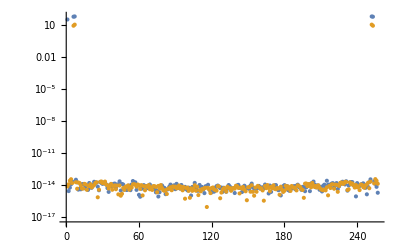

```mathematica
L=12;
m=128;n=2*m+1;
Δx=2.0L/n;
f[x_]:=2+ 7.3 Cos[5π x/L]-7.7 Sin[6π x/L]
x[j_]:=-L+j Δx
fix[n_][m_]:=If[0≤m≤n/2,m, m-n]
h=0.1;
fVec=Table[f[x[j]],{j,1,n}];
fShiftVec=Table[f[x[j]+h],{j,1,n}];
FData=Fourier[fVec];
FShiftData=Fourier[fShiftVec];
ShiftMask=Table[ⅇ^(ⅈ 2π (fix[n][k-1]h)/n),{k,1,n}];
ListLogPlot[{Abs[FData],
Abs[FShiftData-ShiftMask*FData]}
]
```

```mathematica
f[x_]:
```

I can shift the function over by h by simply shifting all the sines and 
u(x+h) 

If I shift all the points in x_j=a+j Δx over by Δx then I get x_(j+1)=a+(j+1) Δx.  Since we are periodi

```mathematica
L=4;
m=256;n=2*m;
Δx=2.0L/n;
c=0.1;
f[x_]:=2+Sin[
]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
ListPlot[fVec,PlotRange->All,DataRange->{-L,L}];
FData=Fourier[fVec];
TabView[{
"All"->ListPlot[{Re[FData],Im[FData],Abs[FData]}, PlotLegends->{"re","im","abs"},
PlotRange->All],
"All-Abs"->ListLogPlot[Abs[FData], PlotLegends->{"abs"},
PlotRange->All],
"All-Arg"->ListPlot[Arg[FData], PlotLegends->{"arg"},
PlotRange->All],
"Low"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{1,20},All},
PlotStyle->PointSize[0.02]],
"High"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{n-20,n},All},
PlotStyle->PointSize[0.02]]
}]
```

12345

```mathematica
c=0.01;
f[x_]:=2+Sin[6π x/L+c]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
ListPlot[fVec,PlotRange->All,DataRange->{-L,L}];
FData=Fourier[fVec];
TabView[{
"Low-Abs"->ListLogPlot[Abs[FData], PlotLegends->{"abs"},
PlotRange->{{1,10},All},
PlotStyle->PointSize[0.02]],
"Low-Arg"->ListPlot[Arg[FData], PlotLegends->{"arg"},
PlotRange->{{1,10},All},
PlotStyle->PointSize[0.02]]
}]
```

12

## Travelling Wave Phase Shifts

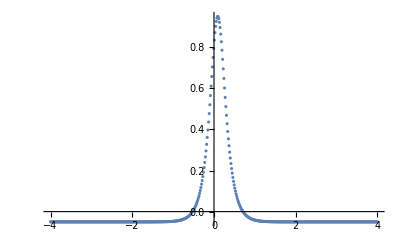

```mathematica
L=4;
m=256;n=2*m;
Δx=2.0L/n;
c=0.1;
f[x_]:=-0.05+Sech[6(x-c)]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
ListPlot[fVec,PlotRange->All,DataRange->{-L,L}]
```

```mathematica
FData=Fourier[fVec];
TabView[{
"All"->ListPlot[{Re[FData],Im[FData],Abs[FData]}, PlotLegends->{"re","im","abs"},
PlotRange->All],
"All-Abs"->ListLogPlot[Abs[FData], PlotLegends->{"abs"},
PlotRange->All],
"All-Arg"->ListPlot[Arg[FData], PlotLegends->{"arg"},
PlotRange->All],
"Low"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{1,20},All},
PlotStyle->PointSize[0.02]],
"High"-> ListPlot[{Re[FData],Im[FData]}, PlotLegends->{"re","im"},
PlotRange->{{n-20,n},All},
PlotStyle->PointSize[0.02]]
}]
```

12345

```mathematica
c=0.01;
fVec=Table[f[x[j]+c],{j,1,n}];
ListPlot[fVec,PlotRange->All,DataRange->{-L,L}];
FData=Fourier[fVec];
TabView[{
"All-Abs"->ListLogPlot[Abs[FData], PlotLegends->{"abs"},
PlotRange->All],
"All-Arg"->ListPlot[Arg[FData], PlotLegends->{"arg"},
PlotRange->All]
}]
```

12